```mathematica
g = 9.80655;
m = 1.0565;

Impulse = 74.3897504622088;
IntegralofImpulse = 308.8587146374167;
burntime = 7.02;

Impulse = 16.839;
IntegralofImpulse = 15.5163001126130;
burntime = 1.65;
AverageForce = Impulse/burntime;

(*F15*)
Impulse=49.2278625190001;
IntegralofImpulse=87.3413889289923;
burntime=3.45;

v =  g*burntime - Impulse/m;
vmax= 5+ v;
vmin = -5 + v;
s0 = -(burntime * v+ IntegralofImpulse/m -g*burntime^2/2);
NumberLinePlot[Abs[v0-g burntime+Impulse/m]<5,{v0,-10,5}];
(*RegionPlot[Abs[s0 + burntime * v0 + IntegralofImpulse/m -g*burntime^2/2]< 5, {v0, vmin,vmax}, {s0, 0,100}]*)
Plot[{-( burntime * ( 5 +(g*burntime - Impulse/k)) + IntegralofImpulse/k -g*burntime^2/2), -( burntime * ( -5 +(g*burntime - Impulse/k)) + IntegralofImpulse/k -g*burntime^2/2), -( burntime * (g*burntime - Impulse/k) + IntegralofImpulse/k -g*burntime^2/2)},{k, 0, 1.1}];
(*Plot[-v0*burntime- .5*(AverageForce/m  - g)* burntime^2, {v0, -15,0}]*)

thrustUp = 0.95;
Impulse = thrustUp * Impulse;
IntegralofImpulse = thrustUp * IntegralofImpulse;
Plot[{-( burntime * ( 5 +(g*burntime - Impulse/k)) + IntegralofImpulse/k -g*burntime^2/2), -( burntime * ( -5 +(g*burntime - Impulse/k)) + IntegralofImpulse/k -g*burntime^2/2), -( burntime * (g*burntime - Impulse/k) + IntegralofImpulse/k -g*burntime^2/2)},{k, 0, 1.1}];


ClearAll["Global`*"]
f[x_] = 0.06322x^4-0.6969x^3+9.705x^2-2.483x+0.1121;
(*f[x_] = 7.389x^2 +0.1201x -0.5509;*)
g = 9.80655;
m = 1.0565;
t = 0;
FullSimplify[Discriminant[f[x]/m -g*x^2/2 + v*(x+h) -g*h*x+s-g*h^2/2, x]];
v0= -5 -g*t;
s0 = 20 - g*t^2/2 -5*t;
Solve[Discriminant[f[x]/m -g*x^2/2 + v0*(x+h) -g*h*x+s0-g*h^2/2, x] ==0, h, PositiveReals];
Discriminant[f[x]/m -g*x^2/2 + v0*(x+h) -g*h*x+s0-g*h^2/2, x];
```

20-5 gamma-4.90328 gamma^2+(-5-9.80655 gamma) t-4.90328 t^2+0.946522 (Piecewise[{{t (-1.713+(8.685-0.245567 t) t), t≤3.45}, {-83.2055+49.4449 t, True}}])

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Greater::nord: Invalid comparison with 2.53758-0.829265 ⅈ attempted.

Greater::nord: Invalid comparison with 2.54251-0.815511 ⅈ attempted.

Greater::nord: Invalid comparison with 2.54747-0.801447 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Part::partw: Part 3 of {Undefined,Undefined} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

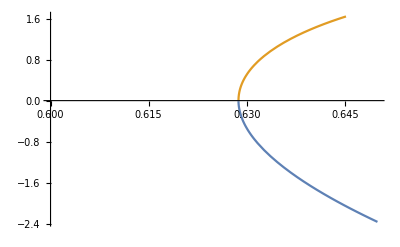

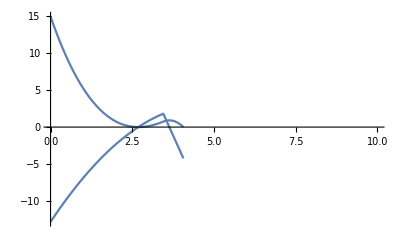

Part::partd: Part specification solution⟦{2,3}⟧ is longer than depth of object.

{}

{1.6818,1.40039}

{{t→2.19853},{t→3.29885}}

```mathematica
ClearAll["Global`*"]
$MaxExtraPrecision=200;
g = 9.80655;
m = 1.0565;
v0 = -5;
s0 = 20;
tm = Solve[s0 + v0*tmax - g*tmax^2/2 ==0, tmax, NonNegativeReals];

vb[gamma_] = v0 - g*gamma;
sb[gamma_] = s0 + v0*gamma - g*gamma^2/2;
Impulse[t_] = -0.7367*t^2 + 17.37*t - 1.713;
Impulse[t_] = FullSimplify[Piecewise[{{ -0.7367*t^2 + 17.37*t - 1.713, 0≤t≤ 3.45}, {-0.7367*3.45^2 + 17.37*3.45 - 1.713, t>3.45}}], t ∈ NonNegativeReals];
Thrust[t_] = FullSimplify[D[Impulse[t], t], t≥ 0];
(*IntegralofImpulse[t_] = 0.06322t^4-0.6969t^3+9.705t^2-2.483t+0.1121;
IntegralofImpulse[t_] = 7.389t^2 + 0.1197t - 0.5504;*)
IntegralofImpulse[t_]  = FullSimplify[Integrate[Impulse[t], t]];
Plot[{ 7.389t^2 + 0.1197t - 0.5504, 0.06322t^4-0.6969t^3+9.705t^2-2.483t+0.1121,  IntegralofImpulse[t]}, {t, -2, 8}];

displacement[t_,gamma_]= IntegralofImpulse[t]/m - g*t^2/2 + vb[gamma]*t + sb[gamma]
(*s[t_,gamma_] = FullSimplify[Piecewise[{{displacement, displacement≥  0}}, Indeterminate],  t ≥ 0 && 0≤ gamma ≤ t /. tm[[1]]];*)
s[t_,gamma_] = Piecewise[{{Undefined, t < 0 ||  gamma < 0}, {displacement[t,gamma], displacement[t,gamma]≥0}}, Undefined];
v[t_,gamma_] = Piecewise[{{Undefined, t < 0 ||  gamma < 0}, {Impulse[t]/m - g*t + vb[gamma], s[t, gamma] ≥ 0}}, Undefined];
(*Integrate[v[t,gamma,s],t]*)
(*solution = Reduce[s[t, gamma] == 0 && 0 ≤ gamma ≤ tmax/.tm, t, Reals]*)
sols = SetPrecision[Solve[s[t, gamma] == 0  && gamma ≤ tmax/.tm[[1]], t, Reals], 200];
(*FullSimplify[Solve[displacement[t, gamma] == 0  &&  0≤ gamma ≤ 0.6 && t ∈ NonNegativeReals, t, Reals]]
FullSimplify[Solve[s[t, gamma] == 0  &&  0.5≤ gamma ≤ 0.6 && t ∈ NonNegativeReals, t, Reals]]
solution = Reduce[s[t, gamma] == 0 && gamma ≤0.6, t, Reals]*)
(*%/. gamma -> 0.01*)
(*%/.(Or[a_&&b_]):>{b,a}//Apply[Piecewise[{##}]&]*)
(*LogicalExpand[%]*)
(*N[%]/.{HoldPattern[And[_[b1_,___,b2_],a==a0_]]:>{a0,{b1,b2}}};
ineqToIntv=HoldPattern[Inequality[m_,Less|LessEqual,s_Symbol,Less|LessEqual,M_]|Inequality[M_,Greater|GreaterEqual,s_Symbol,Greater|GreaterEqual,m_]]:>(s==Interval[{m,M}]);
rules=LogicalExpand[FullSimplify[sols] ]/.ineqToIntv;*)
(*FullSimplify[sols /.(Or[a_&&b_]):>{b,a}//Apply[Piecewise[{##}]&], 0≤ gamma ≤ tmax/.tm]*)
(*Roots[s[t, gamma] == 0 && t ∈ NonNegativeReals && 0≤ gamma ≤ tmax/.tm, t];
Solve[FullSimplify[sols], t, Reals];*)
(*sols = FullSimplify[%,Assumptions->{gamma∈PositiveReals}]*)
(*Piecewise[List@@@Last@@@N@%]*)

(*Solve[Reduce[s[t, 0.3] == 0, t, Reals] , t, PositiveReals]*)
(*sols /. gamma -> .7
Solve[s[t, 0.7] == 0.1, t, Reals]
Solve[displacement[t, 0.7] == 0,t , Reals, WorkingPrecision -> 6000]
displacement[t/. %[[1]], 0.7]
s [t /. %[[1]], 0.7] 
v[sols , gamma]  /. gamma -> .7*)
(*Plot[v[#, gamma /. gamma -> x]& /@ (t /. sols/. gamma ->x/.Undefined->-1),{x, 0, tmax} /. tm[[1]],PlotPoints->100,MaxRecursion->10]*)
(*Solve[s[t, 0.5] == 0, t, Reals]
Solve[displacement[t, 0.5] == 0,t , Reals]*)
fncn[x_] =v[#,x] & /@  (t/.sols /. gamma -> x);
(*ReplaceAll[ Undefined -> 0][(v[#,.3] & /@  (t/.((sols /. gamma -> .3) /. Undefined -> -1)))]*)
Plot[{fncn[x][[1]],fncn[x][[2]], fncn[x][[3]], fncn[x][[4]]}, {x, 0.6,0.65} /. tm[[1]]]
Plot[{s[t, gamma],v[t,gamma]}/. gamma -> 0.6287445370447116, {t, 0, 10},PlotPoints->100,MaxRecursion->10] 
(*solution /. gamma -> 1
v[solution, gamma] /. gamma -> 1*)
vgamma[x_] = Abs[v[solution[[{2, 3}]], gamma] /. gamma -> x] ;
DeleteCases[t/.sols /. gamma -> 0.6287445370447116,Undefined]
Abs[v[#, 0.64]]&/@ DeleteCases[t/.sols /. gamma -> 0.64,Undefined]
sols /. gamma -> 0.64

sols /. gamma -> 0;
Solve[s[t, 0] == 0, t, Reals];
ArgMin[vgamma[x],x ∈ Reals];
```

InterpolatingFunction::dmval: Input value {3.45074} lies outside the range of data in the interpolating function. Extrapolation will be used.

Plot::itraw: Raw object t cannot be used as an iterator.

InterpolatingFunction::dmval: Input value {3.45072} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.45084} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.45006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

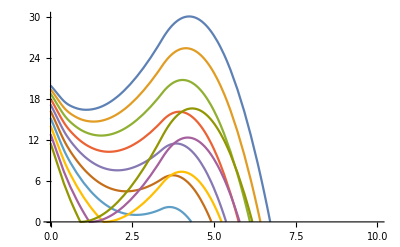

InterpolatingFunction::dmval: Input value {3.45098} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.45044} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.45065} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.45085} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.45003} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.45085} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

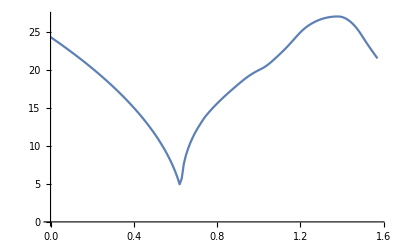

InterpolatingFunction::dmval: Input value {3.4508} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.45075} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.45011} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

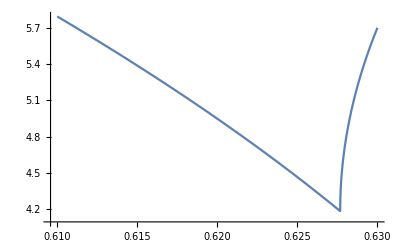

4.18035

0.62767

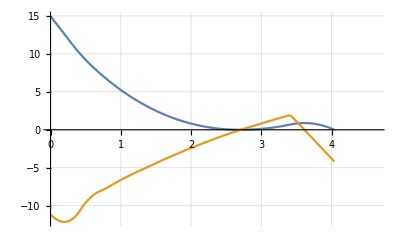

```mathematica
ClearAll["Global`*"]
$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`50."&);
g = 9.80655;
m = 1.0565;
v0 = -5;
s0 = 20;
burntime= 3.45;
tm = Solve[s0 + v0*tmax - g*tmax^2/2 ==0, tmax, NonNegativeReals];

vb[gamma_] := v0 - g*gamma;
sb[gamma_] := s0 + v0*gamma - g*gamma^2/2;

thrustCurve=Flatten[Import["C:\\Users\\rag\\Documents\\GitHub\\EPQ\\Rocket\\F15_Thrust.xlsx"] ,1];
ifun=Interpolation[thrustCurve, InterpolationOrder -> 1];
Plot[ifun[t],{t,0.,3.45}, PlotRange->Full];
model=a + b*t + c*t^2 + d*t^3 + e*t^4 + f*t^5 + gh*t^6 + h*t^7 + i*t^8 + j*t^9;
p = FindFit[thrustCurve, model,{a, b,c,d,e,f,gh,h,i,j} ,t];
Plot[model /. %, {t, 0,3.45}];
Thrust[t_] = Piecewise[{{ifun[t], 0< t < 3.45}}];
(*DSolve[{s''[t]==Thrust[t]/m-g,s'[0] == vb[gamma], s[0] == sb[gamma]},s,{t, 0, ∞}] ;
DSolve[{s''[t]==t/m-g, WhenEvent[s[t]== 0, s'[t] -> 0]},s,{t, 0, 5}];*)
psol = ParametricNDSolve[{s''[t]==Thrust[t]/m-g,s'[0] == vo, s[0] == so, WhenEvent[s[t]== 0,If[t > 3.45, "StopIntegration", s'[t] -> 0]]},{s, s'},{t, 0, ∞}, {vo, so}, "ExtrapolationHandler"->{Indeterminate&,"WarningMessage"->False}, PrecisionGoal-> ∞, MaxStepSize -> 0.001];
h=s/. % ;
v = s' /. psol;
x = 0.645;
Plot[{h[vb[x], sb[x]][t],h[vb[x], sb[x]]'[t]}, {t,0,h[vb[x], sb[x]]["Domain"][[1, 2]]}];
Plot[{vb[y], sb[y]}, {y, 0, 1}];
(*FindRoot[h[vb[x], sb[x]][t],{t,0,0, h[vb[x], sb[x]]["Domain"][[1, 2]]}, WorkingPrecision -> 100];*)
Plot[Evaluate@Table[Tooltip[h[vb[x], sb[x]][t],x],{x,0,1,0.1}],{t,0,10}]
Table[h[vb[x], sb[x]], {x,0.3,1,0.1}];
l = %[[1]];
Plot[l[t], {t, 0,  5.73}];
(*Table[FindRoot[#[t], {t, t0, 0, #["Domain"][[1, 2]]}],{t0,{0, #["Domain"][[1, 2]], 1}}]& /@ Table[h[vb[x], sb[x]], {x,0.3,1,0.1}];
l'/@ (t/. Table[FindRoot[l[t], {t, t0, 0, l["Domain"][[1, 2]]}],{t0,{0, l["Domain"][[1, 2]], 1}}]);*)
velocities = Max[Abs[#' /@ (t/. Table[FindRoot[#[t], {t, t0, 0, #["Domain"][[1, 2]]}],{t0,0, #["Domain"][[1, 2]], 1}])]]& /@ Table[h[vb[x], sb[x]], {x,0,tmax /. tm[[1]],0.01}];
ListLinePlot[Transpose[{Range[0,tmax /. tm[[1]],0.01], %}]]
velocities[[Ordering[velocities, 1][[1]]]];
bestIgnition = Range[0,tmax /. tm[[1]],0.01][[Ordering[velocities, 1][[1]]]];
velo= Max[Abs[#' /@ (t/. Table[FindRoot[#[t], {t, t0, 0, #["Domain"][[1, 2]]}],{t0,0, #["Domain"][[1, 2]], 1}])]]& /@ Table[h[vb[x], sb[x]], {x,bestIgnition - 0.01,bestIgnition+ 0.01,0.00001}];
ListLinePlot[Transpose[{Range[bestIgnition - 0.01,bestIgnition+ 0.01, 0.00001], %}]]
velo[[Ordering[velo, 1][[1]]]]
accurateIgnition = Range[bestIgnition - 0.01,bestIgnition+ 0.01, 0.00001][[Ordering[velo, 1][[1]]]]
Plot[{h[vb[accurateIgnition], sb[accurateIgnition]][t],v[vb[accurateIgnition], sb[accurateIgnition]][t]} , {t,0,h[vb[x], sb[x]]["Domain"][[1, 2]]}, GridLines-> Automatic]
(*Table[h[vb[x], sb[x]], {x,0.3,1,0.1}]
Max[Abs[#' /@ (t/. Table[FindRoot[#[t], {t, t0, 0, #["Domain"][[1, 2]]}],{t0,{0, #["Domain"][[1, 2]], 1}}])]]& /@ {h[vb[x], sb[x]]}*)
(*Plot[FindRoot[h[vb[y], sb[y]][t],{t,0,0, h[vb[y], sb[y]]["Domain"][[1, 2]]}, WorkingPrecision -> 100], {y, 0, .1}]*)
(*Plot[Max[(t /. Table[FindRoot[h[vb[y], sb[y]][t],{t,t0}, WorkingPrecision -> 100],{t0,{0, h[vb[y], sb[y]]["Domain"][[1, 2]], 0.001}}])], {y, 0, 1}]*)
(*Plot[Max[Abs[h[vb[y], sb[y]]'[#]& /@ (t /. Table[FindRoot[h[vb[y], sb[y]][t],{t,t0}, WorkingPrecision -> 50],{t0,{0, h[vb[y], sb[y]]["Domain"][[1, 2]], 0.001}}])]], {y,0,1}]*)

(*FindMinimum[{Max[Abs[#' /@ (t/. Table[FindRoot[#[t], {t, t0, 0, #["Domain"][[1, 2]]}],{t0,{0, #["Domain"][[1, 2]], 1}}])]]& /@ {h[vb[y], sb[y]]}, 0≤ y≤ 1.5}, y]*)
```

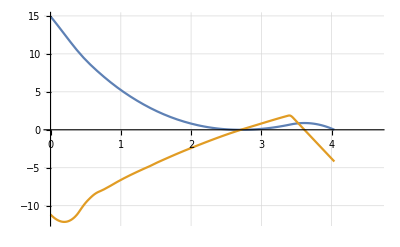

```mathematica
Plot[{h[vb[accurateIgnition], sb[accurateIgnition]][t],v[vb[accurateIgnition], sb[accurateIgnition]][t]} , {t,0,h[vb[x], sb[x]]["Domain"][[1, 2]]}, GridLines-> Automatic]
```

```mathematica
x = 0.061;
(*FindRoot[h[vb[a], sb[a]][t] == 0, {t, 0, 0, h[vb[a], sb[a]]["Domain"][[1,2]]}]/. a-> .64;
Max[Abs[#' /@  Last @@@(Table[FindRoot[#[t], {t, t0, 0, #["Domain"][[1, 2]]}],{t0,0, #["Domain"][[1, 2]], 1}])]]& /@ {h[vb[x], sb[x]]};
Last @@@ Flatten[Table[FindRoot[#[t], {t, t0, 0, #["Domain"][[1, 2]]}, PrecisionGoal-> 50, AccuracyGoal-> 50],{t0,0, #["Domain"][[1, 2]], 1}]& /@{h[vb[x], sb[x]]}];*)
Max[Abs[v[vb[x], sb[x]] /@ Last @@@ Flatten[Table[FindRoot[#[t], {t, t0, 0, #["Domain"][[1, 2]]}],{t0,0, #["Domain"][[1, 2]], 1}]& /@{h[vb[x], sb[x]]}]]]
FindFormula[h[vb[gamma], sb[gamma]]]
f[gamma_] = Max[Abs[v[vb[gamma], sb[gamma]] /@ Last @@@ Flatten[Table[FindRoot[#[t], {t, t0, 0, #["Domain"][[1, 2]]}],{t0,0, #["Domain"][[1, 2]], 1}]& /@{h[vb[gamma], sb[gamma]]}]]]
(*v[vb[x], sb[x]] /@ Flatten[Last @@@(Table[FindRoot[#[t], {t, t0, 0, #["Domain"][[1, 2]]}],{t0,0, #["Domain"][[1, 2]], 1}])& /@{h[vb[x], sb[x]]}]
ReplaceAll[Table[FindRoot[h[vb[a], sb[a]][t], {t, t0, 0, h[vb[a], sb[a]]["Domain"][[1, 2]]}],{t0,0, h[vb[a], sb[a]]["Domain"][[1, 2]], .1} ] , a-> 0.645]
Max[Abs[v[vb[a], sb[a]] /@ Last @@@ (FindRoot[h[vb[a], sb[a]][t] == 0, {t, 0, 0, h[vb[a], sb[a]]["Domain"][[1,2]]}]/. a-> 1)]] /. a-> 1*)
FindMinimum[f[y], {y, 0.645,0, 1}]
Plot[h[vb[1], sb[1]][t], {t, 0, 2}];
```

22.9069

ParametricNDSolve::prange: Invalid non-numeric value -5-9.80655 gamma for parameter vo.

FindFormula::wrgfmt: Argument ParametricFunction[1,«4»,{NDSolve`base$154317,NDSolve`NDSolveParametricFunction[0,{ParametricNDSolve,Internal`Bag[<2>],None,ParametricNDSolve},{{{1,0,0,1,0,0,0,2,0},{0,0,0,0,0,0,0,0,0}},{0,{#1&,#1&,#1&},{0,{t$154311}},{{s},{s},{s}}},None,{{{vo$154309,so$154310},System`Utilities`HashTable[<3>],{},{},{1,2},{Automatic,0,0}},{Automatic,Automatic},None,{}}},{s,s'},{«1»},«1»,{Automatic,Automatic,MachinePrecision,Automatic,Automatic,Automatic,Automatic,None,None,Automatic,«7»,{},{},Automatic,Automatic,None,None,None,{Indeterminate&,WarningMessage→False},Automatic,Automatic},{Cache→True,CacheTableLength→19,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},{},All]}][«1»] at position 1 does not have the right format. Data should be a numerical array of depth less or equal than 2.

FindFormula[ParametricFunction[<>][-5-9.80655 gamma,20-5 gamma-4.90328 gamma^2]]

ParametricNDSolve::prange: Invalid non-numeric value -5-9.80655 gamma for parameter vo.

Part::partd: Part specification «1»⟦1,2⟧ is longer than depth of object.

Table::iterb: Iterator {t0,0,ParametricFunction[1,Internal`Bag[<1>],«3»,{NDSolve`base$154317,NDSolve`NDSolveParametricFunction[0,{ParametricNDSolve,Internal`Bag[<2>],None,ParametricNDSolve},{{{«9»},{«9»}},{0,{«3»},{«2»},{«3»}},None,{{«6»},{«2»},None,{}}},{s,s'},{{Equal[«2»],Equal[«2»],Equal[«2»]},{},{},{},{WhenEvent[«2»]}},{{0.,DirectedInfinity[«1»]}},{Automatic,Automatic,MachinePrecision,Automatic,Automatic,Automatic,Automatic,None,None,Automatic,Automatic,Automatic,Automatic,1/10,1,Automatic,Automatic,{},{},Automatic,Automatic,None,None,None,{«1»&,Rule[«2»]},Automatic,Automatic},{Cache→True,CacheTableLength→19,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},{},All]}][«1»][…]⟦«1»⟧,1} does not have appropriate bounds.

Part::partd: Part specification «1»⟦1,2⟧ is longer than depth of object.

ParametricNDSolve::prange: Invalid non-numeric value -5.-9.80655 gamma for parameter vo.

General::stop: Further output of ParametricNDSolve::prange will be suppressed during this calculation.

Part::partd: Part specification «1»⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FindRoot::srect: Value t0 in search specification {t,t0,0,«1»} is not a number or array of numbers.

Abs[ParametricFunction[<>][-5-9.80655 gamma,20-5 gamma-4.90328 gamma^2][{t,t0,0,ParametricFunction[<>][-5-9.80655 gamma,20-5 gamma-4.90328 gamma^2][Domain]⟦1,2⟧}]]

ParametricNDSolve::prange: Invalid non-numeric value -5-9.80655 y for parameter vo.

Part::partd: Part specification «1»⟦1,2⟧ is longer than depth of object.

FindMinimum::nrnum: The function value {Abs[«1»],Abs[«1»],11.3252,8.95846} is not a real number at {y} = {0.645}.

FindMinimum[f[y],{y,0.645,0,1}]

```mathematica
psol=ParametricNDSolve[{y''[t]+y[t]==3a Sin[y[t]],y[0]==y'[0]==1,α'[t]==Sqrt[1+y[t]^2],α[0]==0},{y,α},{t,0,10},{a}];
b[a][t] = y[a][t] /. psol;
Plot[Evaluate@Table[b[a][t],{a,0,1,.1}],{t,0,10}];
Plot[Evaluate[b[a][10]],{a,0,1},PlotPoints->100];
FindMinimum[b[a][10], {a, 0.72},AccuracyGoal->7];
```

FindMinimum::scdims: Values given in search specification {a,0.72,0,tmax/.tm} do not have consistent dimensions.

FindMinimum[v[vb[a],sb[a]][3.45],{a,0.72,0,tmax/.tm}]

FindMinimum::nrnum: The function value b[0.72][10] is not a real number at {a} = {0.72}.